Modify these as necessary.

```mathematica
importPath="/Users/jackshi/Downloads/result.csv";
exportPath = "/Users/jackshi/Downloads/result.csv";
tf=200;
L=14;
xmin=-50;
xmax=200;
ymin=-100;
ymax=50;
```

```mathematica
numFrames = 500;
```

Import and set up data.

```mathematica
data=Transpose[Import[importPath]];
data2=Transpose[Import[importPath2]];
x0=ListInterpolation[data[[1]],{{0,tf}}];
y0=ListInterpolation[data[[2]],{{0,tf}}];
th0=ListInterpolation[data[[3]],{{0,tf}}];
a1=ListInterpolation[data[[4]],{{0,tf}}];
a2=ListInterpolation[data[[5]],{{0,tf}}];
```

Import::chtype: First argument importPath2 is not a valid file, directory, or URL specification.

```mathematica
th1=th0[#]-a1[#]&;
th2=th0[#]+a2[#]&;
x1=x0[#]-L/2 Cos[th0[#]]-L/2 Cos[th1[#]]&;
y1=y0[#]-L/2 Sin[th0[#]]-L/2 Sin[th1[#]]&;
x2=x0[#]+L/2 Cos[th0[#]]+L/2 Cos[th2[#]]&;
y2=y0[#]+L/2 Sin[th0[#]]+L/2 Sin[th2[#]]&;
```

Check the plots to make sure.

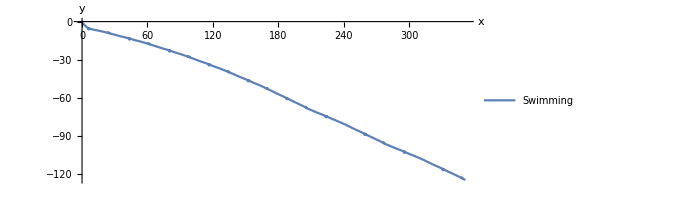

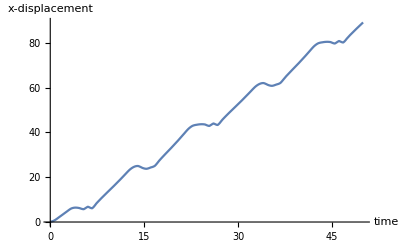

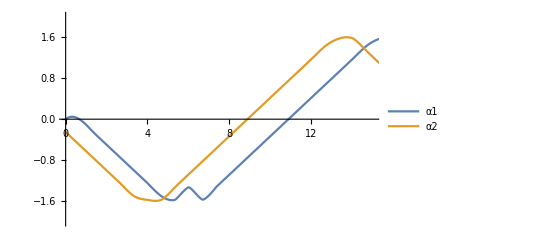

-Graphics-

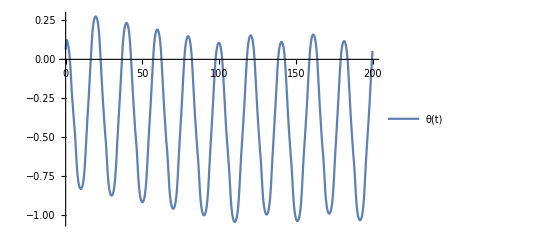

```mathematica
ParametricPlot[{x0[k],y0[k]},
{k,0,tf},AxesLabel->{"x", "y"},  BaseStyle->{FontSize->20},Ticks->Automatic, PlotLegends->{"Swimming", "Wheeled"}]
Plot[{x0[k]},{k,0,tf/4},AxesLabel->{"time","x-displacement"}]
Plot[{a1[k],a2[k]},{k,0,tf}, PlotRange->{{0, 15},{-2, 2}}, PlotLegends->{"α1","α2"},BaseStyle->{FontSize->20},Ticks->Automatic]
Plot[{a3[k],a4[k]},{k,0,tf}, PlotRange->{{0, 15},{-2, 2}}, PlotLegends->{"α1","α2"},BaseStyle->{FontSize->20},Ticks->Automatic]
Plot[{th0[k]},{k,0,tf},PlotLegends->{θ[t]}]
```

```mathematica
|
```

Here are some purely aesthetic parameters.

```mathematica
a=L/2;
b= 18/7;
```

Here are the elements of a 3 D cartoon.

```mathematica
fluid = Graphics[{RGBColor[0, 0.8, 0.8], Rectangle[{xmin,ymin}, {xmax, ymax}]}, Axes -> True];
link[xCenter_, yCenter_, θ_] = Graphics[{White, EdgeForm[Thick], Rotate[Disk[{xCenter,yCenter}, {a, b}], θ, {xCenter,yCenter}]}];
Show[{link[x1[k],y1[k],th1[k]],link[x2[k],y2[k],th2[k]],link[x0[k],y0[k],th0[k]]}/.k->3.2,Boxed->False]
```

-Graphics-

Animate!

```mathematica
frame[k_] := Show[{fluid, link[x0[k],y0[k],th0[k]], link[x1[k],y1[k],th1[k]], link[x2[k],y2[k],th2[k]]}]
frames = Table[frame[k], {k, 0, tf/6, (tf/6)/numFrames}];
ListAnimate[frames]
```

```mathematica
Export[exportPath,frames, ImageResolution->800,Antialiasing->True];
```